# Chiral potential V

## Using the elliptic functions to determine the chiral potentials

## The potential is constructed to depend on the modulus k explicitly

```mathematica
ClearAll["Global`*"]
```

Helper functions

```mathematica
thesispath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][thesispath,name, format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[q,{q,a,b,(b-a)/(n-1)}];
```

Fit parameters

```mathematica
moisfit1={91,9,51};
moisfit2={13.53,101.76,52.94};
moisfit3={89,12,48};
spinvalues={22.5,18.5,14.5};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
magicpower=2; (* use the exponent within the JacobiAmplitude calculation *)
A[k_,mois_]:=N[1/(2*#)&/@mois][[k]];
rad[theta_]:=N[theta*π/180];
j[k_,thetadeg_]:={oddspin*Cos[rad[thetadeg]],oddspin*Sin[rad[thetadeg]]}[[k]];
Afactor[spin_,thetadeg_,mois_]:=A[2,mois](1-j[2,thetadeg]/spin)-A[1,mois];
ufactor[spin_,thetadeg_,mois_]:=(A[3,mois]-A[1,mois])/Afactor[spin, thetadeg, mois];
v0factor[spin_,thetadeg_, mois_]:=-(A[1,mois]*j[1,thetadeg])/Afactor[spin,thetadeg,mois];
modulusk[spin_,thetadeg_,mois_]:=√Abs[ufactor[spin,thetadeg,mois]];
period[modulusk_]:=NIntegrate[1/(√(1-modulusk^2 Sin[t]^2)),{t,0,π/2}];
```

The potential depends on the factors k=√(|u|) and v_0 explicitly

```mathematica
qvalues[spin_,thetadeg_,mois_]:=linspace[-4*period[modulusk[spin,thetadeg,mois]],4*period[modulusk[spin,thetadeg,mois]],200];
V[q_,spin_,thetadeg_,mois_]:=(spin*(spin+1)*modulusk[spin,thetadeg ,mois]^2+v0factor[spin,thetadeg ,mois]^2)*Sin[JacobiAmplitude[q,modulusk[spin,thetadeg ,mois]^magicpower]]^2+(2*spin+1)*v0factor[spin,thetadeg ,mois]*Cos[JacobiAmplitude[q,modulusk[spin,thetadeg ,mois]^magicpower]]*√(1-modulusk[spin,thetadeg ,mois]^2*Sin[JacobiAmplitude[q,modulusk[spin,thetadeg ,mois]^magicpower]]^2);
dvdq[p_,spin_,thetadeg_,mois_]:=D[V[q,spin,thetadeg,mois],q]/.{q->p};
```

Analysis of the period differences between the potential for θ and θ+π

```mathematica
periodtheta[spin_,thetadeg_,mois_]:=period[modulusk[spin,thetadeg,mois]];
periodthetapi[spin_,thetadeg_,mois_]:=period[modulusk[spin,thetadeg+180,mois]];
deltaperiod[spin_,thetadeg_,mois_]:=Abs[periodtheta[spin,thetadeg,mois]-periodthetapi[spin,thetadeg,mois]];
(*periodlines={Graphics[{Red,Thick,Line[{{-2*period[kconst[thetadegfit1]],-100},{-2*period[kconst[thetadegfit1]],100}}]}],
Graphics[{Red,Thick,Line[{{2*period[kconst[thetadegfit1]],-100},{2*period[kconst[thetadegfit1]],100}}]}],
Graphics[{Blue,DotDashed,Line[{{-2*period[kconst[thetadegfit1+180]],-100},{-2*period[kconst[thetadegfit1+180]],100}}]}],
Graphics[{Blue,DotDashed,Line[{{2*period[kconst[thetadegfit1+180]],-100},{2*period[kconst[thetadegfit1+180]],100}}]}]};*)
```

Plot the potential V(q,θ) and V(q,θ+π)

```mathematica
qvalues1=qvalues[22.5,thetadegfit1,moisfit1];
potentialPlot=ListLinePlot[{
Table[{q,V[q,22.5,thetadegfit1,moisfit1]},{q,qvalues1}],
Table[{q,V[q,22.5,thetadegfit1+180,moisfit1]},{q,qvalues1}]},
ImageSize->600,
AspectRatio->0.8,
Frame->True,
Axes->True];
```

Plot the asymmetric potential V_asymm

ℹ️Requires an offset for the q coordinate for both the θ part and the θ+π part

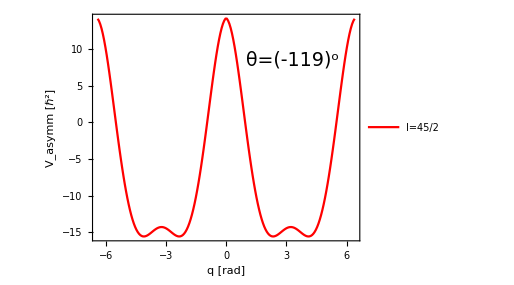

```mathematica
offsetq[q_,spin_,thetadeg_,mois_]:=If[q<=0,
0.5(V[q+deltaperiod[spin,thetadeg,mois],spin,thetadeg,mois]-V[q-deltaperiod[spin,thetadeg,mois],spin,thetadeg+180,mois]),
0.5(V[q-deltaperiod[spin,thetadeg,mois],spin,thetadeg,mois]-V[q+deltaperiod[spin,thetadeg,mois],spin,thetadeg+180,mois])];
asymmetricplot[spin_,thetadeg_,mois_]:=ListLinePlot[{
Table[
{q,offsetq[q,spin,thetadeg,mois]},{q,qvalues1}]},
ImageSize->380,
AspectRatio->0.75,
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"q [rad]","V_asymm [ℏ^2]"},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
PlotStyle->{Red,Thick},
PlotLegends->Placed[{StringTemplate["I=``/2"][Round[2*spin]]},{0.25,0.8}],
Epilog->{Inset[Style[StringTemplate["θ=(``)^o"][thetadeg],Black,FontFamily->"Latin Modern Roman",19],Scaled[{0.75,0.8}]]}];
Show[asymmetricplot[22.5,thetadegfit1,moisfit1]]
```